## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PGMi";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
(*pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef_1/";*)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_MASSpy_r.csv";

mainFolder = "fit_PGMi_MASSpy_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological, Q10];
```

((2pg)^c⇌(3pg)^c)^PGMi

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | Null | 2.9815 | 2.83242
3.13057 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | 0.00021 | 0.0002
0.00022 |  |  | 7 | 30 |  | 
1 | 2pg | 0.000097 | 0.000092
0.000102 |  |  | 7 | 30 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null | 41.7812 | 37.9829
45.5795 |  | 7 | 37 |  | 
1 | 2pg | Null | 18.9914 | 15.1932
22.7897 |  | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {10};
kmPriorities = {1,1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((2pg)^c⇌(3pg)^c)^PGMi

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
10 | 2pg | Null | 2.9815 | 2.83242
3.13057 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | 0.00021 | 0.0002
0.00022 |  |  | 7 | 30 |  | 
1 | 2pg | 0.000097 | 0.000092
0.000102 |  |  | 7 | 30 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null | 41.7812 | 37.9829
45.5795 |  | 7 | 37 |  | 
1 | 2pg | Null | 18.9914 | 15.1932
22.7897 |  | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
Overscript[(3pg)^c⇌(2pg)^c, PGMd]
```

((3pg)^c⇌(2pg)^c)^PGMd

```mathematica
catalyticBranch={"E_PGMi[c] + 2pg[c] <=> E_PGMi[c]&2pg",

				"E_PGMi[c]&2pg <=> E_PGMi[c]&3pg",
				
				"E_PGMi[c]&3pg <=> E_PGMi[c] + 3pg[c]"}; (*Reaction now properly flipped*)


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((PGMi^c)_^+(2pg)^c⇌(PGMi^c&(2pg)^c)_^)^PGMi1,((PGMi^c&(3pg)^c)_^⇌(PGMi^c)_^+(3pg)^c)^PGMi2,((PGMi^c&(2pg)^c)_^⇌(PGMi^c&(3pg)^c)_^)^PGMi3}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PGMi^c)_^+(2pg)^c⇌(PGMi^c&(2pg)^c)_^)^PGMi1,Overscript[(PGMi^c&(3pg)^c)_^⇌(PGMi^c)_^+(3pg)^c, PGMi2],((PGMi^c&(2pg)^c)_^⇌(PGMi^c&(3pg)^c)_^)^PGMi3};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((PGMi^c&(2pg)^c)_^-((PGMi^c&(3pg)^c)_^)/K_PGMi3) Volume_c k_PGMi3^⟶}

Volume_c (-(PGMi^c&(3pg)^c)_^ k_PGMi3^⟵+(PGMi^c&(2pg)^c)_^ k_PGMi3^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
flux = 0.0012546434607581675;
FluxExpression = absoluteFlux /. {metabolite["2pg", "c"] -> 0.000149989144013334,metabolite["3pg","c"]-> 0,
     parameter["PGMi_total"] -> 0.0000285993060080716, parameter["Volume", "c"] -> 1};
```

```mathematica
FluxExpression2 = parameter["v", "PGMi"] /. FluxExpression;
```

```mathematica
enzymeModel
```

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={{3,FluxExpression2,flux,{0.9*flux,1.1*flux}}};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

```mathematica
FilePrint@dataPathList
```

Priority	2pg[c]	3pg[c]	param_PGMi_total	param_pH	param_Temp	FileFlag	Target_Data
10	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	2.98149708
10	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	2.98149708
10	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	2.98149708
10	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	2.98149708
10	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	2.98149708
10	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	2.98149708
10	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	2.98149708
10	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	2.98149708
10	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	2.98149708
10	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	2.98149708
10	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	2.98149708
1	0	0.000021000000000000012	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_3pg.txt"	0.09090909090909095
1	0	0.000033282757041683415	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_3pg.txt"	0.1368068886032101
1	0	0.000052749615061701256	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_3pg.txt"	0.20076000891310197
1	0	0.0000836025058162344	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_3pg.txt"	0.2847472489508014
1	0	0.00013250104234084062	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_3pg.txt"	0.38686317984685703
1	0	0.00021000000000000012	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_3pg.txt"	0.5000000000000001
1	0	0.00033282757041683416	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_3pg.txt"	0.6131368201531433
1	0	0.0005274961506170126	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_3pg.txt"	0.7152527510491988
1	0	0.0008360250581623448	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_3pg.txt"	0.7992399910868984
1	0	0.0013250104234084062	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_3pg.txt"	0.86319311139679
1	0	0.002100000000000001	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_3pg.txt"	0.9090909090909091
1	9.700000000000007e-6	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_2pg.txt"	0.09090909090909097
1	0.00001537346396687282	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_2pg.txt"	0.13680688860321016
1	0.000024365298385642967	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_2pg.txt"	0.200760008913102
1	0.00003861639554368923	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_2pg.txt"	0.2847472489508014
1	0.00006120286241457877	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_2pg.txt"	0.3868631798468571
1	0.00009700000000000008	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_2pg.txt"	0.5000000000000002
1	0.00015373463966872819	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_2pg.txt"	0.6131368201531432
1	0.00024365298385642967	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_2pg.txt"	0.7152527510491988
1	0.0003861639554368927	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_2pg.txt"	0.7992399910868985
1	0.0006120286241457877	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_2pg.txt"	0.8631931113967901
1	0.0009700000000000008	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_2pg.txt"	0.9090909090909091
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	41.781178611280566
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	41.781178611280566
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	41.781178611280566
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	41.781178611280566
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	41.781178611280566
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	41.781178611280566
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	41.781178611280566
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	41.781178611280566
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	41.781178611280566
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	41.781178611280566
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	41.781178611280566
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	18.99144482330935
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	18.99144482330935
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	18.99144482330935
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	18.99144482330935
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	18.99144482330935
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	18.99144482330935
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	18.99144482330935
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	18.99144482330935
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	18.99144482330935
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	18.99144482330935
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	18.99144482330935
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	2pg[c]	3pg[c]	param_PGMi_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	2.9057170391155402
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	2.9057170391155402
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	2.9057170391155402
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	2.9057170391155402
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	2.9057170391155402
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	2.9057170391155402
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	2.9057170391155402
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	2.9057170391155402
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	2.9057170391155402
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	2.9057170391155402
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	2.9057170391155402
1	0	0.000019406103516902634	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_3pg.txt"	0.09090909090909094
1	0	0.00003075660135613467	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_3pg.txt"	0.13680688860321008
1	0	0.00004874592811257811	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_3pg.txt"	0.20076000891310194
1	0	0.0000772570896258239	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_3pg.txt"	0.2847472489508018
1	0	0.0001224442354173262	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_3pg.txt"	0.386863179846857
1	0	0.00019406103516902634	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_3pg.txt"	0.5000000000000001
1	0	0.0003075660135613467	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_3pg.txt"	0.6131368201531432
1	0	0.0004874592811257811	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_3pg.txt"	0.7152527510491988
1	0	0.0007725708962582382	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_3pg.txt"	0.7992399910868984
1	0	0.001224442354173262	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_3pg.txt"	0.8631931113967899
1	0	0.0019406103516902634	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_3pg.txt"	0.9090909090909091
1	0.000011039009643877404	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_2pg.txt"	0.09090909090909098
1	0.000017495651236093885	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_2pg.txt"	0.13680688860321014
1	0.000027728738541759076	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_2pg.txt"	0.20076000891310197
1	0.00004394708895036799	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_2pg.txt"	0.28474724895080133
1	0.00006965144210592128	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_2pg.txt"	0.38686317984685703
1	0.00011039009643877405	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_2pg.txt"	0.5000000000000002
1	0.00017495651236093887	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_2pg.txt"	0.6131368201531434
1	0.0002772873854175908	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_2pg.txt"	0.7152527510491989
1	0.00043947088950368037	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_2pg.txt"	0.7992399910868984
1	0.0006965144210592127	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_2pg.txt"	0.86319311139679
1	0.0011039009643877403	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_2pg.txt"	0.9090909090909092
13	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	37.6237046932756
13	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	37.6237046932756
13	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	37.6237046932756
13	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	37.6237046932756
13	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	37.6237046932756
13	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	37.6237046932756
13	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	37.6237046932756
13	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	37.6237046932756
13	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	37.6237046932756
13	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	37.6237046932756
13	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	37.6237046932756
13	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	19.38709570479622
13	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	19.38709570479622
13	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	19.38709570479622
13	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	19.38709570479622
13	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	19.38709570479622
13	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	19.38709570479622
13	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	19.38709570479622
13	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	19.38709570479622
13	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	19.38709570479622
13	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	19.38709570479622
13	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	19.38709570479622

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Set::partw: Part 3 of {{1,3pg,0.00021,{0.0002,0.00022},{},,7,30,{},{}},{1,2pg,0.000097,{0.000092,0.000102},{},,7,30,{},{}}} does not exist.

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Set::partw: Part 3 of {{1,3pg,0.00021,{0.0002,0.00022},{},,7,30,{},{}},{1,2pg,0.000097,{0.000092,0.000102},{},,7,30,{},{}}} does not exist.

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Set::partw: Part 3 of {{1,3pg,0.00021,{0.0002,0.00022},{},,7,30,{},{}},{1,2pg,0.000097,{0.000092,0.000102},{},,7,30,{},{}}} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	2pg[c]	3pg[c]	param_PGMi_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.000021000000000000012	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_3pg.txt"	0.09090909090909095
1	0	0.000033282757041683415	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_3pg.txt"	0.1368068886032101
1	0	0.000052749615061701256	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_3pg.txt"	0.20076000891310197
1	0	0.0000836025058162344	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_3pg.txt"	0.2847472489508014
1	0	0.00013250104234084062	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_3pg.txt"	0.38686317984685703
1	0	0.00021000000000000012	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_3pg.txt"	0.5000000000000001
1	0	0.00033282757041683416	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_3pg.txt"	0.6131368201531433
1	0	0.0005274961506170126	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_3pg.txt"	0.7152527510491988
1	0	0.0008360250581623448	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_3pg.txt"	0.7992399910868984
1	0	0.0013250104234084062	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_3pg.txt"	0.86319311139679
1	0	0.002100000000000001	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_3pg.txt"	0.9090909090909091
1	9.700000000000007e-6	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_2pg.txt"	0.09090909090909097
1	0.00001537346396687282	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_2pg.txt"	0.13680688860321016
1	0.000024365298385642967	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_2pg.txt"	0.200760008913102
1	0.00003861639554368923	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_2pg.txt"	0.2847472489508014
1	0.00006120286241457877	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_2pg.txt"	0.3868631798468571
1	0.00009700000000000008	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_2pg.txt"	0.5000000000000002
1	0.00015373463966872819	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_2pg.txt"	0.6131368201531432
1	0.00024365298385642967	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_2pg.txt"	0.7152527510491988
1	0.0003861639554368927	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_2pg.txt"	0.7992399910868985
1	0.0006120286241457877	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_2pg.txt"	0.8631931113967901
1	0.0009700000000000008	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_2pg.txt"	0.9090909090909091
13	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	41.781178611280566
13	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	41.781178611280566
13	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	41.781178611280566
13	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	41.781178611280566
13	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	41.781178611280566
13	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	41.781178611280566
13	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	41.781178611280566
13	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	41.781178611280566
13	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	41.781178611280566
13	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	41.781178611280566
13	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt"	41.781178611280566
13	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	18.99144482330935
13	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	18.99144482330935
13	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	18.99144482330935
13	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	18.99144482330935
13	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	18.99144482330935
13	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	18.99144482330935
13	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	18.99144482330935
13	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	18.99144482330935
13	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	18.99144482330935
13	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	18.99144482330935
13	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt"	18.99144482330935

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=10;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	10
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_2pg.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_3pg.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateFor_2pg.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/relRateRev_3pg.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMi_MASSpy_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 7.17240649969
best_fit: 2.89981678115
best_fit: 7.18889609002
best_fit: 2.76778696349
best_fit: 7.27028779359
best_fit: 7.268336083
best_fit: 3.32325925118
best_fit: 2.77092385319
best_fit: 2.76425596877
best_fit: 7.22425767562

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
10 | haldaneRatio_1 | 0.000515412 | 2.6565×10^-7 | 0.00354048 | 0.118748 | 2.9815 | 2.98504
10 | haldaneRatio_1 | 0.000515412 | 2.6565×10^-7 | 0.00354048 | 0.118748 | 2.9815 | 2.98504
10 | haldaneRatio_1 | 0.000515412 | 2.6565×10^-7 | 0.00354048 | 0.118748 | 2.9815 | 2.98504
10 | haldaneRatio_1 | 0.000515412 | 2.6565×10^-7 | 0.00354048 | 0.118748 | 2.9815 | 2.98504
10 | haldaneRatio_1 | 0.000515412 | 2.6565×10^-7 | 0.00354048 | 0.118748 | 2.9815 | 2.98504
10 | haldaneRatio_1 | 0.000515412 | 2.6565×10^-7 | 0.00354048 | 0.118748 | 2.9815 | 2.98504
10 | haldaneRatio_1 | 0.000515412 | 2.6565×10^-7 | 0.00354048 | 0.118748 | 2.9815 | 2.98504
10 | haldaneRatio_1 | 0.000515412 | 2.6565×10^-7 | 0.00354048 | 0.118748 | 2.9815 | 2.98504
10 | haldaneRatio_1 | 0.000515412 | 2.6565×10^-7 | 0.00354048 | 0.118748 | 2.9815 | 2.98504
10 | haldaneRatio_1 | 0.000515412 | 2.6565×10^-7 | 0.00354048 | 0.118748 | 2.9815 | 2.98504
10 | haldaneRatio_1 | 0.000515412 | 2.6565×10^-7 | 0.00354048 | 0.118748 | 2.9815 | 2.98504
1 | relRateRev_3pg | 0.164921 | 0.0271991 | 0.041992 | 46.1912 | 0.0909091 | 0.132901
1 | relRateRev_3pg | 0.154914 | 0.0239983 | 0.0586369 | 42.861 | 0.136807 | 0.195444
1 | relRateRev_3pg | 0.141343 | 0.0199779 | 0.0772244 | 38.466 | 0.20076 | 0.277984
1 | relRateRev_3pg | 0.124142 | 0.0154113 | 0.09422 | 33.089 | 0.284747 | 0.378967
1 | relRateRev_3pg | 0.104106 | 0.0108381 | 0.104796 | 27.0885 | 0.386863 | 0.491659
1 | relRateRev_3pg | 0.082937 | 0.00687854 | 0.105211 | 21.0422 | 0.5 | 0.605211
1 | relRateRev_3pg | 0.0627516 | 0.00393776 | 0.0953129 | 15.5451 | 0.613137 | 0.70845
1 | relRateRev_3pg | 0.0453047 | 0.00205251 | 0.0786443 | 10.9953 | 0.715253 | 0.793897
1 | relRateRev_3pg | 0.0314625 | 0.000989886 | 0.0600498 | 7.51337 | 0.79924 | 0.85929
1 | relRateRev_3pg | 0.0212103 | 0.000449877 | 0.0432035 | 5.00508 | 0.863193 | 0.906397
1 | relRateRev_3pg | 0.0139989 | 0.00019597 | 0.0297808 | 3.27589 | 0.909091 | 0.938872
1 | relRateFor_2pg | 0.248473 | 0.0617388 | 0.0701853 | 77.2038 | 0.0909091 | 0.161094
1 | relRateFor_2pg | 0.231868 | 0.053763 | 0.0965262 | 70.5566 | 0.136807 | 0.233333
1 | relRateFor_2pg | 0.209742 | 0.0439917 | 0.124641 | 62.0847 | 0.20076 | 0.325401
1 | relRateFor_2pg | 0.182298 | 0.0332324 | 0.148521 | 52.159 | 0.284747 | 0.433269
1 | relRateFor_2pg | 0.151109 | 0.0228339 | 0.160993 | 41.6149 | 0.386863 | 0.547856
1 | relRateFor_2pg | 0.118984 | 0.0141572 | 0.157588 | 31.5176 | 0.5 | 0.657588
1 | relRateFor_2pg | 0.0890724 | 0.0079339 | 0.139577 | 22.7644 | 0.613137 | 0.752714
1 | relRateFor_2pg | 0.063737 | 0.0040624 | 0.113064 | 15.8076 | 0.715253 | 0.828317
1 | relRateFor_2pg | 0.043953 | 0.00193187 | 0.0851223 | 10.6504 | 0.79924 | 0.884362
1 | relRateFor_2pg | 0.0294704 | 0.000868507 | 0.0606078 | 7.02135 | 0.863193 | 0.923801
1 | relRateFor_2pg | 0.0193665 | 0.00037506 | 0.0414565 | 4.56021 | 0.909091 | 0.950547
1 | absRateRev | 0.0515135 | 0.00265364 | 5.26173 | 12.5935 | 41.7812 | 47.0429
1 | absRateRev | 0.0515135 | 0.00265364 | 5.26173 | 12.5935 | 41.7812 | 47.0429
1 | absRateRev | 0.0515135 | 0.00265364 | 5.26173 | 12.5935 | 41.7812 | 47.0429
1 | absRateRev | 0.0515135 | 0.00265364 | 5.26173 | 12.5935 | 41.7812 | 47.0429
1 | absRateRev | 0.0515135 | 0.00265364 | 5.26173 | 12.5935 | 41.7812 | 47.0429
1 | absRateRev | 0.0515135 | 0.00265364 | 5.26173 | 12.5935 | 41.7812 | 47.0429
1 | absRateRev | 0.0515135 | 0.00265364 | 5.26173 | 12.5935 | 41.7812 | 47.0429
1 | absRateRev | 0.0515135 | 0.00265364 | 5.26173 | 12.5935 | 41.7812 | 47.0429
1 | absRateRev | 0.0515135 | 0.00265364 | 5.26173 | 12.5935 | 41.7812 | 47.0429
1 | absRateRev | 0.0515135 | 0.00265364 | 5.26173 | 12.5935 | 41.7812 | 47.0429
1 | absRateRev | 0.0515135 | 0.00265364 | 5.26173 | 12.5935 | 41.7812 | 47.0429
1 | absRateFor | 0.435526 | 0.189683 | 32.7793 | 172.6 | 18.9914 | 51.7707
1 | absRateFor | 0.435526 | 0.189683 | 32.7793 | 172.6 | 18.9914 | 51.7707
1 | absRateFor | 0.435526 | 0.189683 | 32.7793 | 172.6 | 18.9914 | 51.7707
1 | absRateFor | 0.435526 | 0.189683 | 32.7793 | 172.6 | 18.9914 | 51.7707
1 | absRateFor | 0.435526 | 0.189683 | 32.7793 | 172.6 | 18.9914 | 51.7707
1 | absRateFor | 0.435526 | 0.189683 | 32.7793 | 172.6 | 18.9914 | 51.7707
1 | absRateFor | 0.435526 | 0.189683 | 32.7793 | 172.6 | 18.9914 | 51.7707
1 | absRateFor | 0.435526 | 0.189683 | 32.7793 | 172.6 | 18.9914 | 51.7707
1 | absRateFor | 0.435526 | 0.189683 | 32.7793 | 172.6 | 18.9914 | 51.7707
1 | absRateFor | 0.435526 | 0.189683 | 32.7793 | 172.6 | 18.9914 | 51.7707
1 | absRateFor | 0.435526 | 0.189683 | 32.7793 | 172.6 | 18.9914 | 51.7707
3 | customRatio_1 | 0.0541247 | 0.00292948 | 0.000147011 | 11.7174 | 0.00125464 | 0.00110763
3 | customRatio_1 | 0.0541247 | 0.00292948 | 0.000147011 | 11.7174 | 0.00125464 | 0.00110763
3 | customRatio_1 | 0.0541247 | 0.00292948 | 0.000147011 | 11.7174 | 0.00125464 | 0.00110763
3 | customRatio_1 | 0.0541247 | 0.00292948 | 0.000147011 | 11.7174 | 0.00125464 | 0.00110763
3 | customRatio_1 | 0.0541247 | 0.00292948 | 0.000147011 | 11.7174 | 0.00125464 | 0.00110763
3 | customRatio_1 | 0.0541247 | 0.00292948 | 0.000147011 | 11.7174 | 0.00125464 | 0.00110763
3 | customRatio_1 | 0.0541247 | 0.00292948 | 0.000147011 | 11.7174 | 0.00125464 | 0.00110763
3 | customRatio_1 | 0.0541247 | 0.00292948 | 0.000147011 | 11.7174 | 0.00125464 | 0.00110763
3 | customRatio_1 | 0.0541247 | 0.00292948 | 0.000147011 | 11.7174 | 0.00125464 | 0.00110763
3 | customRatio_1 | 0.0541247 | 0.00292948 | 0.000147011 | 11.7174 | 0.00125464 | 0.00110763
3 | customRatio_1 | 0.0541247 | 0.00292948 | 0.000147011 | 11.7174 | 0.00125464 | 0.00110763

```mathematica
{"/Users/guest/Desktop/internship stuff/MASSef/data","/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input","/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/output"}
```

{/Users/guest/Desktop/internship stuff/MASSef/data,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/output}

### Simulated Data and Best Fit Data Plot

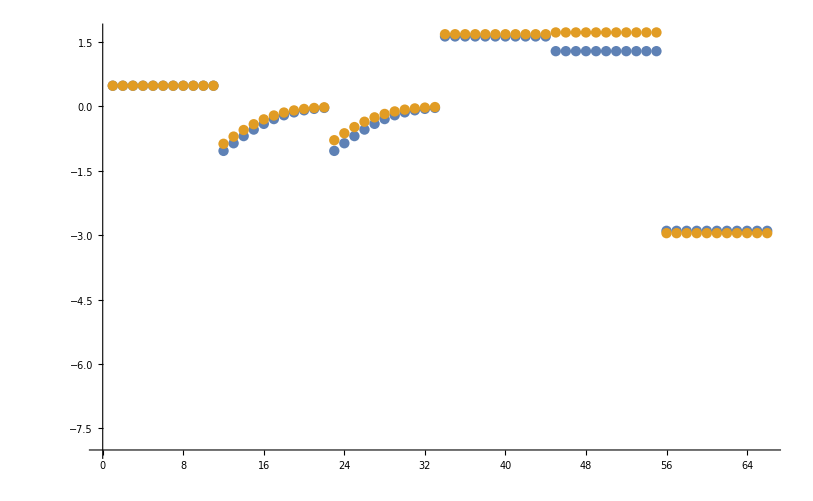

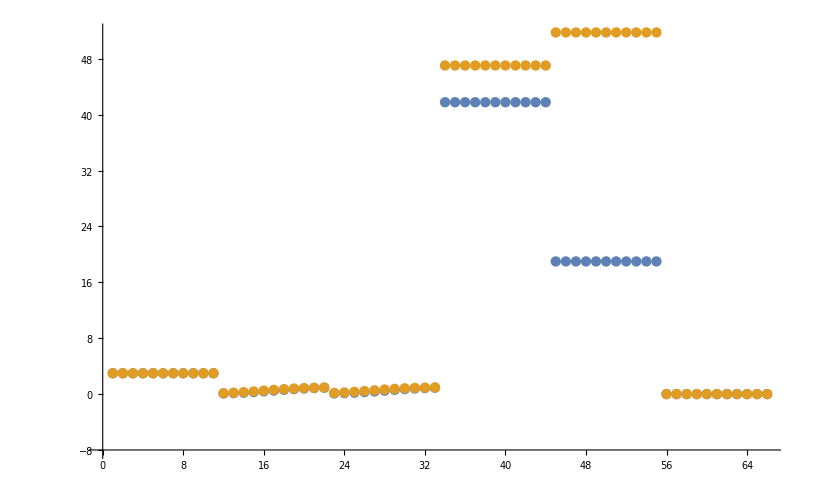

```mathematica
dataSetI=3;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

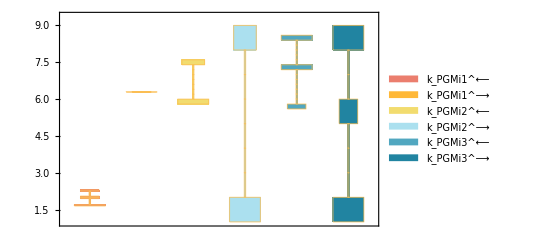

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[1;;5,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

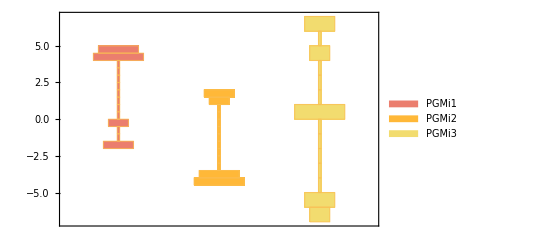

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

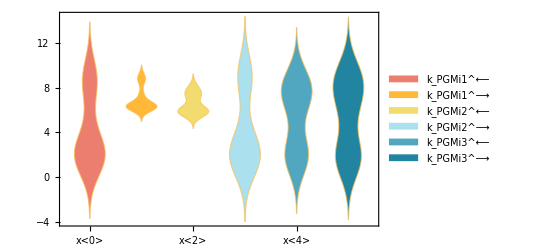

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

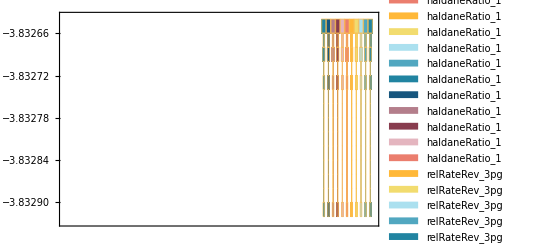

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

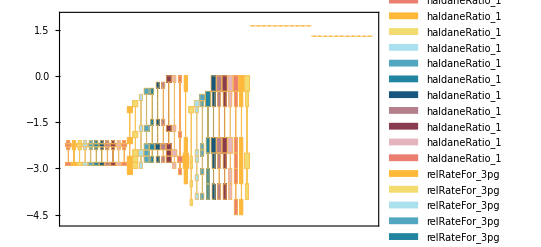

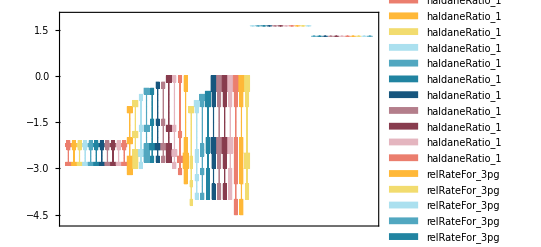

#### Cluster Parameters

```mathematica
(*clusters=FindClusters[Log10[filteredDataListRed[[All,2]]],Method->{"Agglomerate","Linkage"->"Complete","SignificanceTest"->{"Gap","Tolerance"->0.0001}}];(**)*)
clusters=FindClusters[Log10[filteredDataList[[1;;6,2]]],Method->{"Optimize","Iterations"->2}];
medianParamCluster=Table[Median[clusters[[cluster,All,param]]],{cluster,Length[clusters]},{param,Length[clusters[[1,1]]]}](*Switch to log space and use mean?*);
clusterSqdRes=Table[(clusters[[cluster,paramSet,param]]-medianParamCluster[[cluster,param]])^2,{cluster,Length[clusters]},{paramSet,Length[clusters[[cluster]]]},{param,Length[clusters[[1,1]]]}];
clusterSSE=Table[Total[clusterSqdRes[[cluster,paramSet]]],{cluster,Length[clusterSqdRes]},{paramSet,Length[clusterSqdRes[[cluster]]]}];
bestClusterSSE=Table[SortBy[clusterSSE[[cluster]],Less],{cluster,Length[clusterSSE]}][[All,1]];
finalClusterParams={};
Table[If[clusterSSE[[cluster,paramSet]]==bestClusterSSE[[cluster]],finalClusterParams=Append[finalClusterParams,clusters[[cluster,paramSet]]]],{cluster,Length[clusterSSE]},{paramSet,Length[clusterSSE[[cluster]]]}];
```

#### Print Representative Parameter Sets for Each Cluster (Optional)

```mathematica
TableForm[finalClusterParams]
```

7.49616 | 8.37024 | 5.68272 | 1.6719 | 1.22906 | 4.78981
1.22828 | 5.6632 | 5.69368 | 5.51251 | 7.09249 | 3.26277

#### Parameter Cluster Plots (Optional)

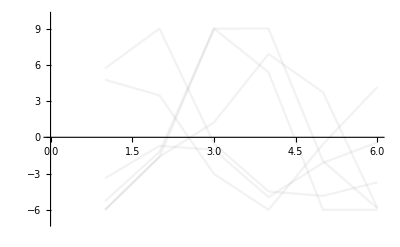

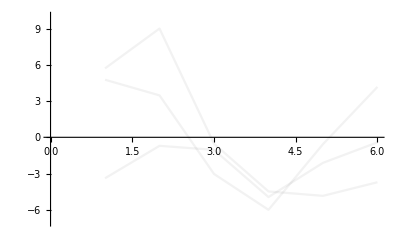
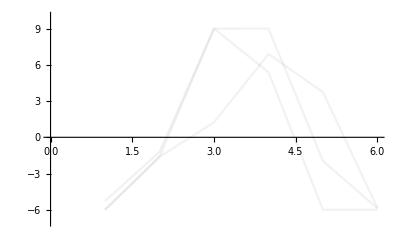

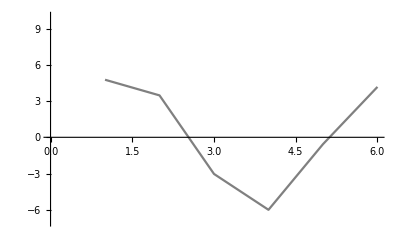
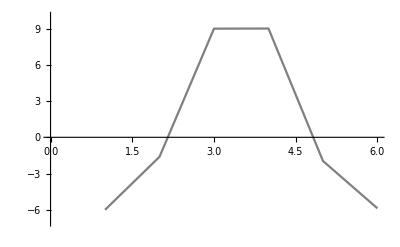

```mathematica
ListPlot[Log10[filteredDataList[[1;;6,2]]],"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]](*All parameter sets*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]]&/@clusters
(*All parameter set clusters*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[1,Gray]]&/@finalClusterParams(*Representative parameter sets*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

data value | predicted value | error in %
0.00021 | 0.000136996 | 34.7637
0.000097 | 0.0000505111 | 47.9267

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
41.7812 | 47.0429 | 12.5935
18.9914 | 51.7707 | 172.6

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
2.9815 | 2.98504 | 0.118748

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
2.9815 | 2.98504 | 0.118748

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

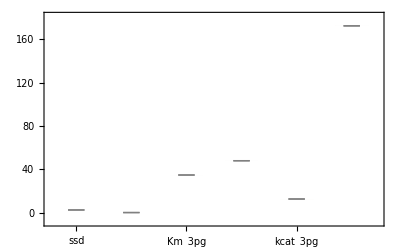

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

## Export data

```mathematica
directoryExport = "/Users/guest/Desktop/internship stuff/MASSef/examples/"
CreateDirectory[directoryExport<>ToLowerCase[rxnName]]
indexLastGoodFit =10;
```

/Users/guest/Desktop/internship stuff/MASSef/examples/

CreateDirectory::filex: /Users/guest/Desktop/internship stuff/MASSef/examples/pgmi already exists.

$Failed

```mathematica
rateConstsString = ToString/@rateConstsSub[[All,1]];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_labels_"<>ToLowerCase[rxnName]<>".txt",rateConstsString]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pgmi\rateconst_labels_pgmi.txt

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\S_"<>ToLowerCase[rxnName]<>".txt",S[enzymeModel]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pgmi\S_pgmi.txt

```mathematica
ToString/@getSpecies[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\species_"<>ToLowerCase[rxnName]<>".txt",ToString/@getSpecies[enzymeModel]]
```

{E_PGMi[c],E_PGMi[c]&2pg,2pg[c],3pg[c],E_PGMi[c]&3pg}

/Users/guest/Desktop/internship stuff/MASSef/examples/pgmi\species_pgmi.txt

```mathematica
ToString/@getReactions[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\reactions_"<>ToLowerCase[rxnName]<>".txt",ToString/@getReactions[enzymeModel]]
```

{PGMi1: 2pg[c] + E_PGMi[c] <=> E_PGMi[c]&2pg,PGMi2: E_PGMi[c]&3pg <=> 3pg[c] + E_PGMi[c],PGMi3: E_PGMi[c]&2pg <=> E_PGMi[c]&3pg}

/Users/guest/Desktop/internship stuff/MASSef/examples/pgmi\reactions_pgmi.txt

```mathematica
solEnz = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/enzSol_"<>rxnName<>"_.m"];
```

```mathematica
speciesStrings = ToString/@solEnz[[All,1]]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_labels_"<>ToLowerCase[rxnName]<>".txt",ToString/@solEnz[[All,1]]];
```

{E_PGMi[c],E_PGMi[c]&2pg,E_PGMi[c]&3pg}

```mathematica
pythonSubList = Thread[Variables[solEnz[[1,2]]]->(ToString/@Variables[solEnz[[1,2]]])];
ToPython[solEnz[[1,2]]/.pythonSubList]
Do[
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_"<>speciesStrings[[i]]<>"_"<>ToLowerCase[rxnName]<>".txt",ToPython[solEnz[[i,2]]/.pythonSubList]];,{i,1,Length[solEnz]}]
```

-((-(k_PGMi1_rev*k_PGMi2_fwd*param_PGMi_total) - k_PGMi2_fwd*k_PGMi3_fwd*param_PGMi_total - k_PGMi1_rev*k_PGMi3_rev*param_PGMi_total)/(2pg(c)*k_PGMi1_fwd*k_PGMi2_fwd + k_PGMi1_rev*k_PGMi2_fwd + 3pg(c)*k_PGMi1_rev*k_PGMi2_rev + 2pg(c)*k_PGMi1_fwd*k_PGMi3_fwd + k_PGMi2_fwd*k_PGMi3_fwd + 3pg(c)*k_PGMi2_rev*k_PGMi3_fwd + 2pg(c)*k_PGMi1_fwd*k_PGMi3_rev + k_PGMi1_rev*k_PGMi3_rev + 3pg(c)*k_PGMi2_rev*k_PGMi3_rev))

```mathematica
(*NEED TO GRAB THE RATE CONST DATA FROM CLUSTERS*)
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_clusters_"<>ToLowerCase[rxnName]<>".txt",filteredDataList[[1;;indexLastGoodFit,2]]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pgmi\rateconst_clusters_pgmi.txt

```mathematica
solRateEq = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/absoluteFlux_"<>rxnName<>"_.m"];
```

```mathematica
pythonSubList = Thread[Variables[solRateEq[[2]]]->(ToString/@Variables[solRateEq[[2]]])];
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateLaw_"<>ToLowerCase[rxnName]<>".txt",ToPython[solRateEq[[2]]/.pythonSubList]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pgmi\rateLaw_pgmi.txt